# Writing Efficient Code and Debugging

## An Elementary Introduction to Debugging in the Wolfram Language

You can find a video with the very basics of debugging in the Wolfram Language here which is part of the Elementary Introduction to Wolfram Language. It covers:

Syntax color corrections,

With

Echo

Monitor

Sow

Reap

Alternatively you can check the Tuning and debugging Guide in the documentation

## TreeForm of Expressions

Recall that everything in the Wolfram Language is an expression. That is something of the form head[param1, param2,...,paramn].

Each of the parameters in itself is also an expression, so it is useful to breakdown the expression tree by using TreeForm.

```mathematica
dataTree={{1,1,1},{{2,2},{3,3}}};
```

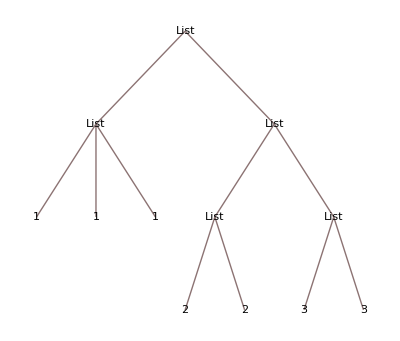

```mathematica
TreeForm[dataTree]
```

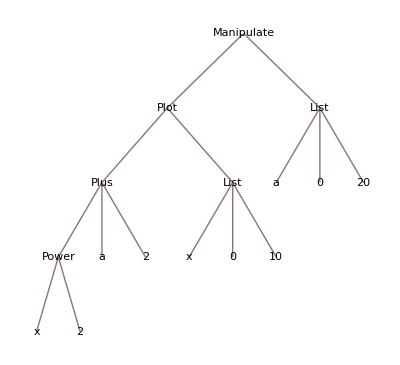

```mathematica
TreeForm[Manipulate[Plot[x^2+a+2,{x,0,10}],{a,0,20}]]
```

The TreeForm is a way of looking at an expression from the root  down, but with longer more complicated expressions it is often more useful to go from the leaf up. You can do so by repeatedly clicking on the node in the expression, or repeatedly pressing  Ctrl+..

The fact that everything is an expression is very useful to reverse engineer objects in the Wolfram Language you can use the FullForm function to see what the Kernel receives (I like to think of it as “in the purest form”)

```mathematica
FullForm[]
```

Manipulate[Plot[Plus[Power[x,2],a,2],List[x,0,10],Rule[PlotRange,List[0,120]]],List[List[a,18.6],0,20]]

Or you can use the InputForm function to see the common way to write it in Wolfram Language code (i.e. with common abbreviations)

```mathematica
InputForm[]
```

Manipulate[Plot[x^2 + a + 2, {x, 0, 10}, PlotRange -> {0, 120}], {{a, 0.}, 0, 20}]

## Useful Functions

#### PrintTemporary

PrintTemporary as its name suggests temporarily prints the expression inside of it and then disappears when the calculation is done

For example the regular result of the code below is giving a list of 5 elements

```mathematica
Table[n,{n,5}]
```

{1,2,3,4,5}

Adding PrintTemporary (and a pause of 1 second to make it visible to the human eye) shows what number the algorithm is adding to the list

```mathematica
Table[(temporary=PrintTemporary[n];Pause[1];n),{n,5}]
```

{1,2,3,4,5}

You can always delete the PrintTemporary as it comes along

```mathematica
Table[(temporary=PrintTemporary[n];Pause[1];NotebookDelete[temporary];n),{n,5}]
```

{1,2,3,4,5}

#### Monitor

Monitor does exactly what the code above does in just a by letting you choose the expression to monitor, which is n in the following code.

```mathematica
Monitor[Table[(Pause[1];n),{n,1,5}],n]
```

{1,2,3,4,5}

For a more computationally demanding procedure we can see the progress.

```mathematica
Table[Factor[x^n-1];,{n,10000}]~Monitor~n
```

$Aborted

#### Abort /Interrupt

To interrupt a computation that is going on you can use Alt + ,. To Abort a computation you can use Alt+.. Note that you can resume an interrupted computation but not an aborted one.

#### Sow and Reap

Sow and Reap are covered in the EIWL video, but as their name suggests, Sow picks up expressions inside of it. If there is a Reap around it then it will give a list with first element the result of the computation and second element the expressions that were “sowed”.

```mathematica
Reap[Total[Table[Sow[n]^2,{n,10}]]]
```

{385,{{1,2,3,4,5,6,7,8,9,10}}}

#### AbsoluteTiming

If you are interested in real computation time  you can use the AbsoluteTiming function

```mathematica
Clear[f]
```

```mathematica
MapIndexed[{First[#2],#1}&,{a,b,c,d,e}]//AbsoluteTiming
```

{0.0000245,{{1,a},{2,b},{3,c},{4,d},{5,e}}}

```mathematica
(v={};
For[i=1,i<=Length[{a,b,c,d,e}],i++,AppendTo[v,{i,{a,b,c,d,e}[[i]]}]];
v)//AbsoluteTiming
```

{0.0000433,{{1,a},{2,b},{3,c},{4,d},{5,e}}}

```mathematica
AbsoluteTiming[Map[(Pause[1];f[#])&,{a,b,c,d,e}]]
```

{5.00561,{f[a],f[b],f[c],f[d],f[e]}}

With the appropriate computations you can use parallel computation to speed things up.

```mathematica
AbsoluteTiming[ParallelMap[(Pause[1];f[#])&,{a,b,c,d,e}]]
```

{2.04936,{f[a],f[b],f[c],f[d],f[e]}}

#### Throw/Catch

Throw and Catch work very similar to Sow and Reap, with the difference being that as soon as Throw gets computed it “throws” that value and Catch takes it.

```mathematica
Catch[Do[If[i!>10^10,Throw[i]],{i,100}]]
```

14

#### Return

```mathematica
f[x_]:=(If[x>5,Return[a]];x+3)
```

```mathematica
f[3]
```

6

```mathematica
f[6]
```

a

#### Break

When a program encounters a Break inside any  loops (Do, Table, For, While...) it terminates said loop

```mathematica
Do[Print[i];If[i>2,Break[]],{i,10}]
```

1

2

3

#### Continue

Alternatively if you would like to skip a round in the loop you can use the Continue function to do so.

```mathematica
Do[If[EvenQ[i],Continue[]];Print[i],{i,10}]
```

1

3

5

7

9

#### Echo

Echo is useful to print out messages into the notebook.

```mathematica
i=0
```

0

```mathematica
{a,b,c,d,c,a,c,b}/.c-> (i++;Echo[i,"replacement"];f)
```

replacement 1

{a,b,f,d,f,a,f,b}

```mathematica
{a,b,c,d,c,a,c,b}/.c:> (i++;Echo[i,"replacement"];f)
```

replacement 2

replacement 3

replacement 4

{a,b,f,d,f,a,f,b}

#### Trace

When you want to follow the steps of a given computation you can use Trace.

```mathematica
5*13+1 ==6*11
```

True

```mathematica
Trace[ 5*13+1 ==6*11]
```

{{{5 13,65},65+1,66},{6 11,66},66==66,True}

Note that it does not work with built in functions.

```mathematica
Trace[Det[{{1,2},{3,4}}]]
```

{Det[{{1,2},{3,4}}],-2}

## Benchmarking

The following is not documented and requires that we load an outside Context namely the GeneralUtilities package to utilize the BenchmarkPlot. More so than AbsoluteTiming it gives you a more involved computation on how the time an algorithm takes relates to the size of it inputs

```mathematica
makeList[n_] := Module[{tmp={}},
	Do[AppendTo[tmp, i], {i, n}];
	tmp
]
```

```mathematica
makeList[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range,makeList}, Identity,"IncludeFits"->True]
```

-Graphics-

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Times,Power}, Identity,"IncludeFits"->True]
```

-Graphics-